# Q1 a)

```mathematica
eqn1=kon*R*L-koff*Rs==0
```

kon L R-koff Rs==0

#### Rearrange equation 3 to solve for Y*, Y*=Ys

```mathematica
Solve[v3*Y/(k3+Y)==v4*Ys/(k4+Ys),Ys]
```

{{Ys→-(k4 v3 Y)/(-k3 v4+v3 Y-v4 Y)}}

```mathematica
Solve[eqn1,Rs]
```

{{Rs→(kon L R)/koff}}

#### Rearrange equation 3 to solve for X*, X*=Xs

```mathematica
eqn2=V1*X/(K1+X)-V2*Xs/(K2+Xs)==0;
```

```mathematica
Solve[eqn2,Xs]
```

{{Xs→-(K2 V1 X)/(-K1 V2+V1 X-V2 X)}}

```mathematica
Solution to Quadratic expression for x*
```

#### Plug in the expressions for x* and y* that I derived on pages 1 & 2 of handwritten notes

```mathematica
eqn6=-Κ2*α1(1-xs)/((α1-1)*(1-xs)-Κ1)==xs
```

-((1-xs) α1 Κ2)/((1-xs) (-1+α1)-Κ1)==xs

```mathematica
Solve[eqn6,xs]
```

{{xs→(-1+α1-Κ1-α1 Κ2-√(-4 (1-α1) α1 Κ2+(-1+α1-Κ1-α1 Κ2)^2))/(2 (-1+α1))},{xs→(-1+α1-Κ1-α1 Κ2+√(-4 (1-α1) α1 Κ2+(-1+α1-Κ1-α1 Κ2)^2))/(2 (-1+α1))}}

#### The final solution for x* is x*=(-1+α1-Κ1-α1 Κ2+√(-4 (1-α1) α1 Κ2+(-1+α1-Κ1-α1 Κ2)^2))/(2 (-1+α1))

## Solution to Quadratic expression for y*

```mathematica
eqn5=-α2*Κ4(1-ys)/((α2-1)(1-ys)-Κ3)==ys
```

-((1-ys) α2 Κ4)/((1-ys) (-1+α2)-Κ3)==ys

```mathematica
Solve[eqn5,ys]
```

{{ys→(-1+α2-Κ3-α2 Κ4-√(-4 (1-α2) α2 Κ4+(-1+α2-Κ3-α2 Κ4)^2))/(2 (-1+α2))},{ys→(-1+α2-Κ3-α2 Κ4+√(-4 (1-α2) α2 Κ4+(-1+α2-Κ3-α2 Κ4)^2))/(2 (-1+α2))}}

#### The final solution for y*=(-1+α2-Κ3-α2 Κ4+√(-4 (1-α2) α2 Κ4+(-1+α2-Κ3-α2 Κ4)^2))/(2 (-1+α2))

#### Part b) Plug in K1=K2=K3=K4=K, V1/V2=5*θB, and V3/V4=10x*. Also plug in θB as 1/(KD+1), so you can graph vs Kd

```mathematica
Solve[eqn6,xs]/.{Κ1->Κ,Κ2->Κ,Κ3->Κ,Κ4->Κ,α1->5*θB,α2->10*xs}/.{θB->(1/(ΚD+1))}
```

{{xs→(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD)-√(-(20 Κ (1-5/(1+ΚD)))/(1+ΚD)+(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD))^2))/(2 (-1+5/(1+ΚD)))},{xs→(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD)+√(-(20 Κ (1-5/(1+ΚD)))/(1+ΚD)+(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD))^2))/(2 (-1+5/(1+ΚD)))}}

#### set x to the + version of the x* answer above for graphing and computation purposes:

```mathematica
x=(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD)+√(-(20 Κ (1-5/(1+ΚD)))/(1+ΚD)+(-1-Κ+5/(1+ΚD)-(5 Κ)/(1+ΚD))^2))/(2 (-1+5/(1+ΚD)));
```

#### Plug in K1=K2=K3=K4=K, V1/V2=5*θB, and V3/V4=10x*. Also plug in θB as 1/(KD+1), so you can graph vs Kd

```mathematica
Solve[eqn5,ys]/.{Κ1->Κ,Κ2->Κ,Κ3->Κ,Κ4->Κ,α1->5*θB,α2->10*xs}/.{θB->(1/(ΚD+1))}
```

{{ys→(-1+10 xs-Κ-10 xs Κ-√(-40 (1-10 xs) xs Κ+(-1+10 xs-Κ-10 xs Κ)^2))/(2 (-1+10 xs))},{ys→(-1+10 xs-Κ-10 xs Κ+√(-40 (1-10 xs) xs Κ+(-1+10 xs-Κ-10 xs Κ)^2))/(2 (-1+10 xs))}}

```mathematica
y=1/(2 (-1+10 xs))(-1+10 xs-Κ-10 xs Κ+√(-40 (1-10 xs) xs Κ+(-1+10 xs-Κ-10 xs Κ)^2))/.xs->x;
```

#### In order to graph these plots as the output vs 1/Kd, I needed to replace Kd with β.

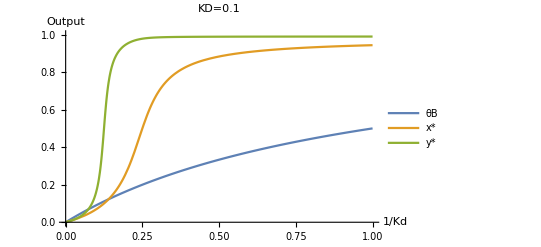

```mathematica
P1=Plot[{(1/(ΚD+1)/.ΚD->1/β),(x/.{Κ->0.1,ΚD->1/β}),(y/.{Κ->0.1,ΚD->1/β})},{β,0,1},PlotLegends->{"θB","x*","y*"},PlotRange->{0,1},PlotLabel->"KD=0.1",AxesLabel->{"1/Kd","Output"}]
```

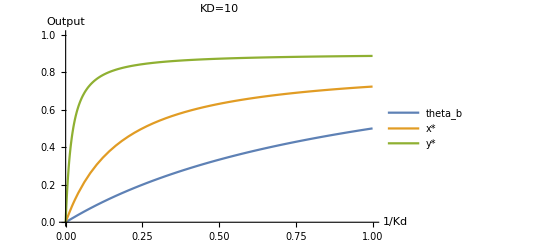

-Graphics-

-Graphics-

```mathematica
P2=Plot[{(1/(ΚD+1)/.ΚD->1/β),(x/.{Κ->10,ΚD->1/β}),(y/.{Κ->10,ΚD->1/β})},{β,0,1},PlotLegends->{"theta_b","x*","y*"},PlotRange->{0,1},PlotLabel->"KD=10",AxesLabel->{"1/Kd","Output"}]
```

## Part c) First solve for κ=0.1 The goal is to fit the hill function to data

```mathematica
xk01=(x/.{Κ->.1,ΚD->1/β});
```

```mathematica
yk01=(y/.{Κ->.1,ΚD->1/β});
```

```mathematica
θBk01=(1/(ΚD+1)/.ΚD->1/β);
```

#### Start by creating matrices of data from the graph, so we can later fit the hill function to this data

```mathematica
xk01hilldata=Reap[For[i=1,i<11,i++,Sow[(i/10)];Sow[(xk01/.β->(i/10))]];][[2,1]]~Partition~2//N
```

{{0.1,0.0696155},{0.2,0.273791},{0.3,0.688819},{0.4,0.833333},{0.5,0.883095},{0.6,0.907545},{0.7,0.922004},{0.8,0.931543},{0.9,0.938303},{1.,0.943343}}

```mathematica
yk01hilldata=Reap[For[i=1,i<11,i++,Sow[(i/10)];Sow[(yk01/.β->(i/10))]];][[2,1]]~Partition~2;
```

```mathematica
θBk01hilldata=Reap[For[i=1,i<10000,i++,Sow[(i/100)];Sow[(θBk01/.β->(i/100))]];][[2,1]]~Partition~2;
```

#### Fit the hill function to the data

```mathematica
FindFit[xk01hilldata,β^n/(Kd+β^n),{Kd,n},β]
```

{Kd→0.0145545,n→3.06904}

#### For x*, n=3.1

```mathematica
xk01hillfit=β^n/(Kd+β^n)/.FindFit[xk01hilldata,β^n/(Kd+β^n),{Kd,n},β]
```

β^3.06904/(0.0145545+β^3.06904)

```mathematica
FindFit[yk01hilldata,β^n/(Kd+β^n),{Kd,n},β]
```

{Kd→1.4081×10^-6,n→6.55674}

#### For y*, n=6.6

```mathematica
yk01hillfit=β^n/(Kd+β^n)/.FindFit[yk01hilldata,β^n/(Kd+β^n),{Kd,n},β]
```

β^6.55674/(1.4081×10^-6+β^6.55674)

```mathematica
FindFit[θBk01hilldata,β^n/(Kd+β^n),{Kd,n},β]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{Kd→1.,n→1.}

#### For θB, n=1 Plot the Hill functions to compare results

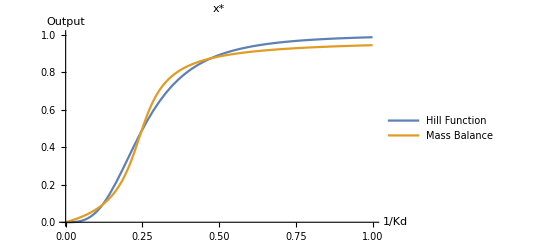

```mathematica
Plot[{xk01hillfit,(x/.{Κ->0.1,ΚD->1/β})},{β,0,1},PlotRange->{0,1},PlotLegends->{"Hill Function","Mass Balance"},PlotLabel->"x*",AxesLabel->{"1/Kd","Output"}]
```

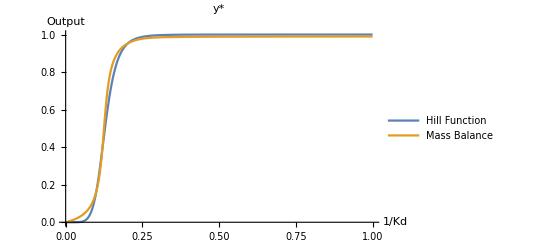

```mathematica
Plot[{yk01hillfit,(y/.{Κ->0.1,ΚD->1/β})},{β,0,1},PlotRange->{0,1},PlotLegends->{"Hill Function","Mass Balance"},PlotLabel->"y*",AxesLabel->{"1/Kd","Output"}]
```

## κ=10 Use equation from notes to find Hill coefficient, n.

```mathematica
-Graphics-
-Graphics-
```

-Graphics-

-Graphics-

#### Create new functions for when K=10

```mathematica
xk10=(x/.{Κ->10,ΚD->1/β});
```

```mathematica
yk10=(y/.{Κ->10,ΚD->1/β});
```

```mathematica
θBk10=(1/(ΚD+1)/.ΚD->1/β);
```

#### Since x* and y* never reach 1, I want to take 0.9 of their maximum output. Take the limit to find the maximum values of x* and y*

```mathematica
xmax=Limit[xk10,β->Infinity]//N
```

0.842194

```mathematica
ymax=Limit[yk10,β->Infinity]//N
```

0.900898

```mathematica
Limit[θBk10,β->Infinity]//N
```

1.

#### Solve for the 10% and 90% values for x*, y*, and θB

```mathematica
NSolve[xk10==0.9*xmax,β]
```

{{β→1.4772}}

```mathematica
NSolve[xk10==0.1*xmax,β]
```

{{β→0.0203141}}

```mathematica
Pcxs=(β/.NSolve[xk10==0.9*xmax,β])/(β/.NSolve[xk10==0.1*xmax,β])
```

{72.7181}

```mathematica
nxs=Log[81]/Log[Pcxs]
```

{1.02516}

#### n for x* is 1.02

```mathematica
NSolve[yk10==0.9*xmax,β]
```

{{β→0.0968466}}

```mathematica
NSolve[yk10==0.1*xmax,β]
```

{{β→0.00221276}}

```mathematica
Pcys=(β/.NSolve[yk10==0.9*xmax,β])/(β/.NSolve[yk10==0.1*xmax,β])
```

{43.7672}

```mathematica
nys=Log[81]/Log[Pcys]
```

{1.1629}

#### n for y* is 1.2

```mathematica
NSolve[θBk10==0.9*xmax,β]
```

{{β→3.13179}}

```mathematica
NSolve[θBk10==0.1*xmax,β]
```

{{β→0.0919646}}

```mathematica
PcθB=(β/.NSolve[θBk10==0.9*xmax,β])/(β/.NSolve[θBk10==0.1*xmax,β])
```

{34.0543}

```mathematica
nθB=Log[81]/Log[PcθB]
```

{1.24561}

#### n for θB=1.2

## Part D) Κ=0.1

```mathematica
PercentForm[Abs[((xk01/.β->0.1)-(xk01/.β->0.15))/(xk01/.β->0.1)]]
```

101.8%

```mathematica
PercentForm[Abs[((yk01/.β->0.1)-(yk01/.β->0.15))/(yk01/.β->0.1)]]
```

402.6%

```mathematica
PercentForm[Abs[((θBk01/.β->0.1)-(θBk01/.β->0.15))/(θBk01/.β->0.1)]]
```

43.48%

## Κ=10

```mathematica
PercentForm[Abs[((xk10/.β->0.1)-(xk10/.β->0.15))/(xk10/.β->0.1)]]
```

27.97%

```mathematica
PercentForm[Abs[((yk10/.β->0.1)-(yk10/.β->0.15))/(yk10/.β->0.1)]]
```

5.657%

```mathematica
PercentForm[Abs[((θBk10/.β->0.1)-(θBk10/.β->0.15))/(θBk10/.β->0.1)]]
```

43.48%

## Part e)

Compared to hyperbolic/michaelian growth, ultrasensitive/0th-order response has sharper response to an input. -Graphics-
As we see in these graphs above, as n increases, the signal is amplified. Whereas, when n decreases, the signal is attenuated.

If we look at the plots in part b, θB has the slowest response, then x, then y has the sharpest response. The signal gets amplified from θB to x to y.

K=10 has a sharper response than K=0.1 so as K increases, we get a more sensitive circuit. If we want to amplify the circuit and increase sensitivity, we should be tuning K to be larger.
K0.1 is more sensitive than k10 case, as seen my the graph. By tunign value of K, you can control senstivity as discussed above

```mathematica
P1
```

-Graphics-

```mathematica
P2
```

-Graphics-